```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

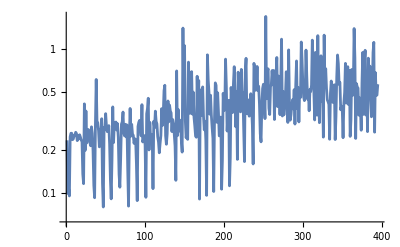

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q1EkG→134.226,Q2EkG→-162.46,Q3EkG→127.664,Q4EkG→93.1193,Q5EkG→-11.2378,Q6EkG→-149.925,S1ELkG→51.5245,S2ELkG→-14585.5,S3ELkG→-1958.27,S3ERkG→-1258.09,S2ERkG→-7174.82,S1ERkG→2084.72,PDrive_mean_x→-0.0000536827,PDrive_mean_y→1.466×10^-7,PDrive_sigma_x→0.0000248384,PDrive_sigma_y→0.0000150957,PDrive_mean_xp→-0.000595723,PDrive_mean_yp→2.732×10^-7,PDrive_xCost→0.0000591505,PDrive_yCost→0.0000150965,PDrive_totalCost→0.0000371235,PDrive_emitSI90_x→2.9552×10^-6,PDrive_emitSI90_y→9.5652×10^-6,PDrive_zLen→0.0000113267,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000345029,PWitness_mean_y→1.16×10^-7,PWitness_sigma_x→0.0000353783,PWitness_sigma_y→6.8426×10^-6,PWitness_mean_xp→-0.000689704,PWitness_mean_yp→-3.85×10^-7,PWitness_xCost→0.0000494173,PWitness_yCost→6.8436×10^-6,PWitness_totalCost→0.0000281305,PWitness_emitSI90_x→0.000148817,PWitness_emitSI90_y→6.6732×10^-6,PWitness_zLen→0.0000617525,PWitness_zCentroid→991.332,bunchSpacing→-0.0000188835,transverseCentroidOffset→0.0000191799,maximizeMe→1.67735|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q1EkG : 134.2262335567
Q2EkG : -162.4602924394
Q3EkG : 127.6644266971
Q4EkG : 93.1192560655
Q5EkG : -11.2377651467
Q6EkG : -149.9245307996
S1ELkG : 51.5244577836
S2ELkG : -14585.5414145922
S3ELkG : -1958.2680756063
S3ERkG : -1258.0866456881
S2ERkG : -7174.8185541442
S1ERkG : 2084.717946452
PDrive_mean_x : -0.0000536827
PDrive_mean_y : 1.466e-7
PDrive_sigma_x : 0.0000248384
PDrive_sigma_y : 0.0000150957
PDrive_mean_xp : -0.0005957231
PDrive_mean_yp : 2.732e-7
PDrive_xCost : 0.0000591505
PDrive_yCost : 0.0000150965
PDrive_totalCost : 0.0000371235
PDrive_emitSI90_x : 2.9552e-6
PDrive_emitSI90_y : 9.5652e-6
PDrive_zLen : 0.0000113267
PDrive_zCentroid : 991.3318133765
PWitness_mean_x : -0.0000345029
PWitness_mean_y : 1.16e-7
PWitness_sigma_x : 0.0000353783
PWitness_sigma_y : 6.8426e-6
PWitness_mean_xp : -0.0006897041
PWitness_mean_yp : -3.85e-7
PWitness_xCost : 0.0000494173
PWitness_yCost : 6.8436e-6
PWitness_totalCost : 0.0000281305
PWitness_emitSI90_x : 0.0001488169
PWitness_emitSI90_y : 6.6732e-6
PWitness_zLen : 0.0000617525
PWitness_zCentroid : 991.331794493
bunchSpacing : -0.0000188835
transverseCentroidOffset : 0.0000191799
maximizeMe : 1.6773515145

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000191798

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
```

{Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
]
```

FittedModel[…]

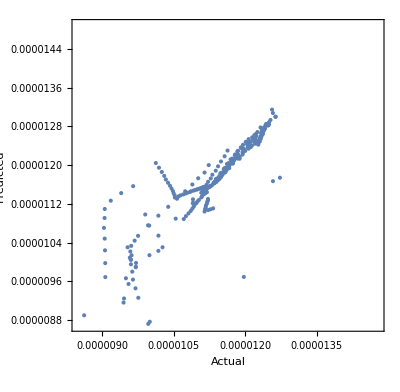

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVars
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{Q1EkG→Indeterminate,Q2EkG→Indeterminate,Q3EkG→Indeterminate,Q4EkG→Indeterminate,Q5EkG→Indeterminate,Q6EkG→Indeterminate,S1ELkG→Indeterminate,S1ERkG→Indeterminate,S2ELkG→Indeterminate,S2ERkG→Indeterminate,S3ELkG→Indeterminate,S3ERkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
Q1EkG | 1 | 4.357×10^-10 | 4.357×10^-10 | 141.232 | 6.24546×10^-28
Q2EkG | 1 | 2.33594×10^-10 | 2.33594×10^-10 | 75.7191 | 9.89637×10^-17
Q3EkG | 1 | 7.40469×10^-9 | 7.40469×10^-9 | 2400.22 | 8.66781×10^-167
Q4EkG | 1 | 1.38441×10^-9 | 1.38441×10^-9 | 448.755 | 1.98702×10^-66
Q5EkG | 1 | 1.25541×10^-13 | 1.25541×10^-13 | 0.0406938 | 0.840237
Q6EkG | 1 | 2.94275×10^-12 | 2.94275×10^-12 | 0.953889 | 0.32935
S1ELkG | 1 | 1.36508×10^-12 | 1.36508×10^-12 | 0.44249 | 0.506325
S1ERkG | 1 | 1.34375×10^-11 | 1.34375×10^-11 | 4.35576 | 0.0375464
S2ELkG | 1 | 1.34295×10^-12 | 1.34295×10^-12 | 0.435316 | 0.50979
S2ERkG | 1 | 4.94602×10^-11 | 4.94602×10^-11 | 16.0324 | 0.0000748288
S3ELkG | 1 | 1.07728×10^-12 | 1.07728×10^-12 | 0.349198 | 0.554917
S3ERkG | 1 | 3.36119×10^-12 | 3.36119×10^-12 | 1.08953 | 0.297236
Error | 382 | 1.17847×10^-9 | 3.08501×10^-12 |  | 
Total | 394 | 1.071×10^-8 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Plot::plln: Limiting value LinearModelFit[{{133.935,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},{140.631,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},{133.935,-170.213,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},«6»,{133.935,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},«385»},{Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,«2»},{Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,«2»}]«1»«10»] in {x,LinearModelFit[«1»][Response],LinearModelFit[{{133.935,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},{140.631,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},{133.935,-170.213,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},«6»,{133.935,-162.107,127.387,93.3149,-11.2134,-148.68,51.4125,2082.54,-14553.9,-7159.23,«3»},«385»},«1»,{Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,«2»}][Response]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[x,{x,Min[lm[Response]],Max[lm[Response]]},PlotStyle→Red]].

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

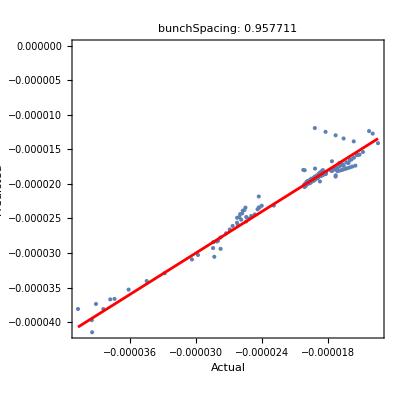
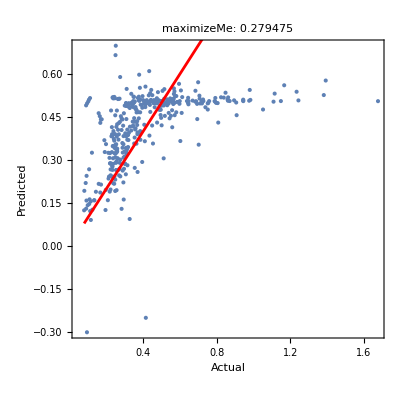
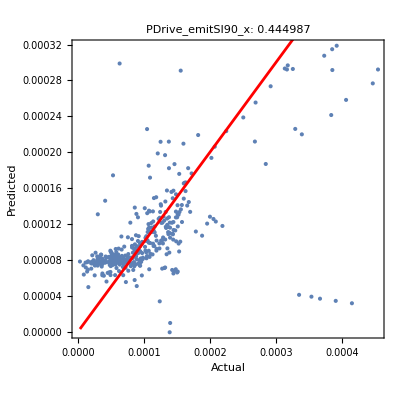
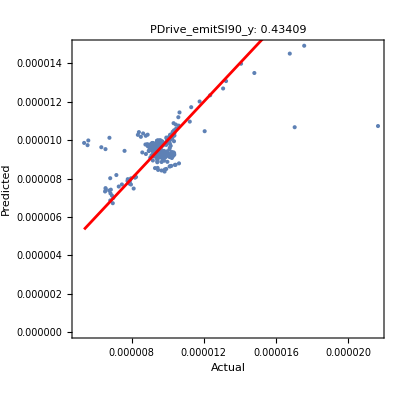
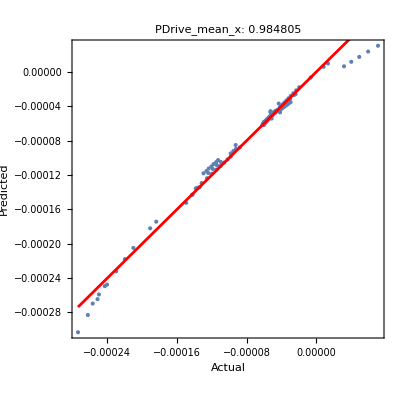
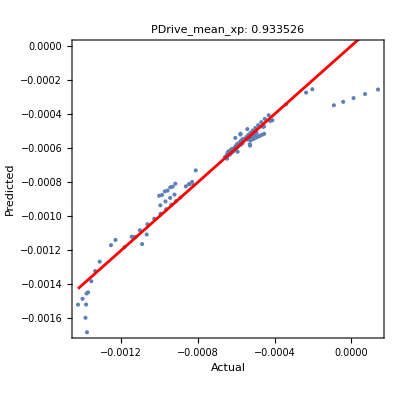
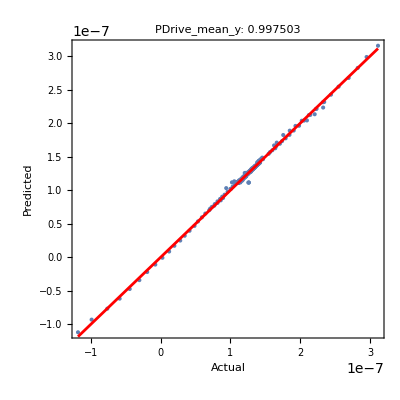
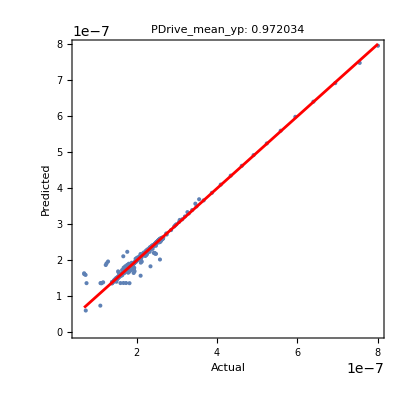
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```